```mathematica
NS["study_overlearningsimple1"]
```

```mathematica
label="testsimple5npc_100_5.csv";scores=Flatten@Import["avgscores_"<>label];
lev=Flatten@Import["avglogev_"<>label];
pro=T@Import["avgprobs_"<>label];
surpr=Flatten@Import["avgsurprise_"<>label];
hit=Flatten@Import["avghit_"<>label];

sdscores=Flatten@Import["sdscores_"<>label];
sdlev=Flatten@Import["sdlogev_"<>label];
sdpro=Import["sdprobs_"<>label];
sdsurpr=Flatten@Import["sdsurprise_"<>label];
sdhit=Flatten@Import["sdhit_"<>label];

ffreqs=(#/Total@#)&@Flatten@Import["avgfreqs_"<>label];sdffreqs=(#/Total@#)&@Flatten@Import["sdfreqs_"<>label];
(*ffreqs=(#/Total/@#)&@Import["finalfreqs_"<>label];*)
ofreqs=Flatten@Import["targetfreqs_"<>label];
nsamples=Length@scores
```

100

```mathematica
nn=Sqrt[500];
```

```mathematica
{ofreqs,ffreqs}//N
```

{{0.333333,0.333333,0.333333},{0.346,0.34,0.314}}

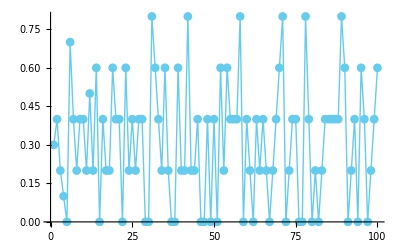

```mathematica
ListPlot[scores,Joined->True,PlotRange->All,PlotMarkers->Auto]
```

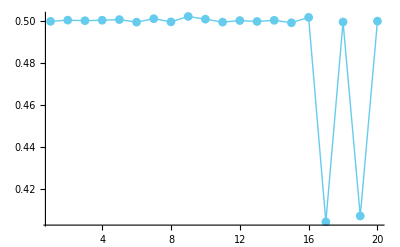

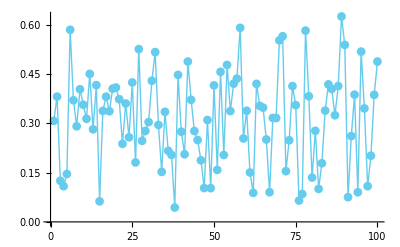

```mathematica
ListPlot[hit,Joined->True,PlotRange->All,PlotMarkers->Auto]
```

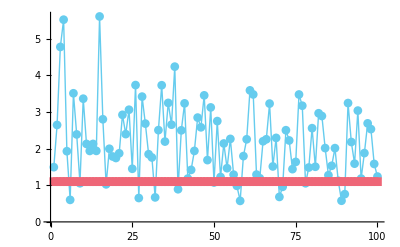

```mathematica
ListPlot[{surpr,-Table[Log@(1/3),{nsamples}]},GridLines->None,Joined->True,PlotRange->All,PlotMarkers->Auto]
```

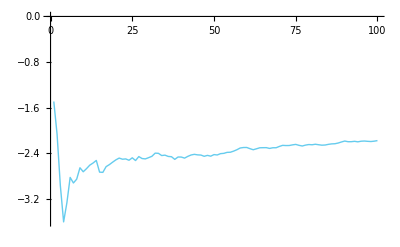

```mathematica
ListPlot[lev/Range@Length@lev,Joined->True,PlotRange->All]
```

```mathematica
(* define a parametric family for a 3-outcome space *)
```

```mathematica
(* used for testsimple3np *)expsum[t_]=Table[(1+10*KroneckerDelta[s,1])*Exp[t*s],{s,{0,2,1}}];
z[t_]=Total@expsum[t];
prob[t_]=Simplify[expsum[t]/z[t]]
```

{1/(1+11 ⅇ^t+ⅇ^(2 t)),ⅇ^(2 t)/(1+11 ⅇ^t+ⅇ^(2 t)),(11 ⅇ^t)/(1+11 ⅇ^t+ⅇ^(2 t))}

```mathematica
(* used for testsimple4np *)expsum[t_]=Table[(1+5*KroneckerDelta[s,1])*Exp[t*s],{s,{0,2,1}}];
z[t_]=Total@expsum[t];
prob[t_]=Simplify[expsum[t]/z[t]]
```

{1/(1+6 ⅇ^t+ⅇ^(2 t)),ⅇ^(2 t)/(1+6 ⅇ^t+ⅇ^(2 t)),(6 ⅇ^t)/(1+6 ⅇ^t+ⅇ^(2 t))}

```mathematica
(* coords transfs to plot the two-distribution space *)
```

```mathematica
trmatrix=T[{{1,0},{0,0},{1/2,Sqrt[3]/2}}];proj[p_]:=trmatrix.p;

plotfreqs[freqs_]:=Block[{nfreqs=(#/Total@#)&@Flatten@freqs},Graphics[{{PointSize@Large,red,Point[proj@nfreqs]}}]];
plotcfreqs[freqs_]:=Block[{nfreqs=(#/Total@#)&@Flatten@freqs},Graphics[{{Thick,red,Circle[proj@nfreqs,0.02]}}]];
sp1={Black,Thin,Line[T[trmatrix][[{1,2,3,1}]]]};
```

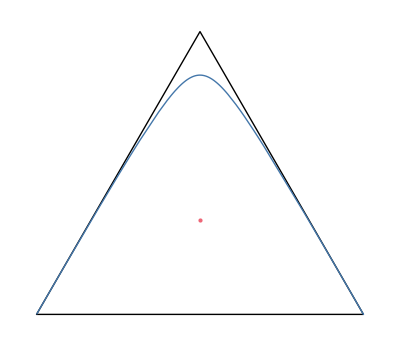

```mathematica
pplot1=ParametricPlot[proj@prob[t],{t,-100,100},Axes->None,PlotRange->All,AspectRatio->Auto,PlotStyle->{Thick,purpleblue}];

doms={Graphics[{sp1}],pplot1};
Show[{doms,plotfreqs[ofreqs]},PlotRange->All]
```

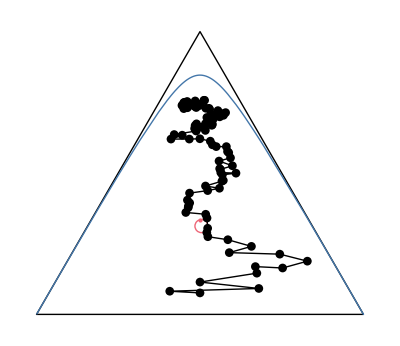

```mathematica
subrange=Round[Range[1,nsamples,nsamples/nsamples]];rplot1=ListPlot[Table[proj@pro[[i]],{i,subrange}],Axes->None,PlotRange->All,PlotStyle->Black,Joined->True,PlotMarkers->Auto];
Show[{doms,plotfreqs@ofreqs,plotcfreqs@ffreqs,rplot1},PlotRange->All]
```

```mathematica
expdf0["overlearning2"]
```

overlearning2.pdf

```mathematica
gtest=Import["allsurprises_"<>label];Dimensions[gtest]
```

{15,163840}

```mathematica
{mi=Min[gtest],ma=Max[gtest]}
```

{0.0384908,9.88559}

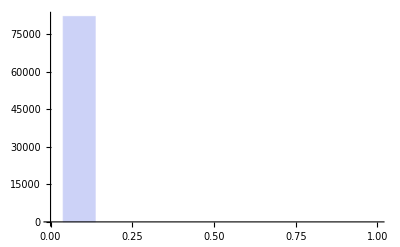

```mathematica
Histogram[gtest[[2,;;]],{mi,ma,(ma-mi)/100},PlotRange->{{0,1},All}]
```

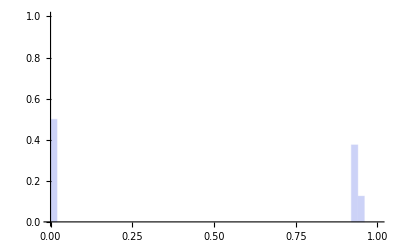

```mathematica
Histogram[Exp@-gtest[[4,;;]],{0,1,1/50},"Probability",PlotRange->{{0,1},{0,1}}]
```

```mathematica
gtest[[10,1;;10]]
```

$Aborted[]

```mathematica
Table[{i,Mean@Exp@-gtest[[i,;;]],GeometricMean@Exp@-gtest[[i,;;]]},{i,15}]//MF
```

(1 | 0.478351 | 0.478351
2 | 0.479148 | 0.0114572
3 | 0.473056 | 0.0609967
4 | 0.470677 | 0.0143143
5 | 0.463643 | 0.0446159
6 | 0.458384 | 0.0184201
7 | 0.451218 | 0.0432496
8 | 0.444408 | 0.0236921
9 | 0.436611 | 0.0459306
10 | 0.42946 | 0.0298425
11 | 0.418127 | 0.0489662
12 | 0.411829 | 0.036115
13 | 0.401121 | 0.0538648
14 | 0.394557 | 0.0425463
15 | 0.383679 | 0.0585788)